```mathematica
(*QMC vs DFT numbers so far*)
(*0.656855889312E+03-35.7492
0.700632335374E+03-35.6979
0.746311811773E+03-35.6309*)
```

```mathematica
(*Sam's results in au*)
eQMCHartree={-35.7492,-35.6979,-35.6309}
vQMCBohr={656.855889312,700.632335374,746.311811773}

(*Sam's results in eV-Ang*)
eQMCeV=27.2114*eQMCHartree
eQMCeVref=eQMCeV-eQMCeV[[1]]
vQMCAng=vQMCBohr*(0.529177249^3)
vQMCalatt=vQMCAng^(1/3)
qmc=Transpose@{vQMCalatt,eQMCeVref}
```

{-35.7492,-35.6979,-35.6309}

{656.856,700.632,746.312}

{-972.786,-971.39,-969.567}

{0.,1.39594,3.21911}

{97.336,103.823,110.592}

{4.6,4.7,4.8}

{{4.6,0.},{4.7,1.39594},{4.8,3.21911}}

```mathematica
qhaNormal={"QHA_normal/e-v.dat","QHA_normal/volume_expansion.dat","QHA_normal/volume-temperature.dat","QHA_normal/gruneisen-temperature.dat","QHA_normal/gibbs-temperature.dat","QHA_normal/bulk_modulus-temperature.dat","QHA_normal/Cp-temperature.dat","QHA_normal/dsdv-temperature.dat"};
swatch={PlotLegends->SwatchLegend[{"Defective","Perfect"},left],ImageSize->400,Joined->True,PlotStyle->{Thick}};normal=Table[ReadList[qhaNormal[[i]],{Number, Number}],{i,1,8}];
lda=Transpose@{(Transpose[normal[[1]]][[1]])^(1/3)/2,Transpose[normal[[1]]][[2]]}
```

{{4.575,-673.839},{4.658,-675.71},{4.725,-674.609},{4.8,-670.996},{4.875,-665.213}}

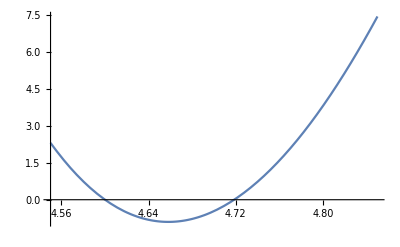

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

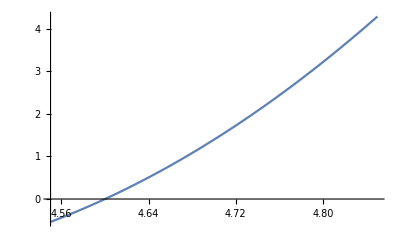

```mathematica
Plot[Interpolation[lda][x]-Interpolation[lda][4.6],{x,4.55,4.85}]
Plot[Interpolation[qmc][x],{x,4.55,4.85}]
```

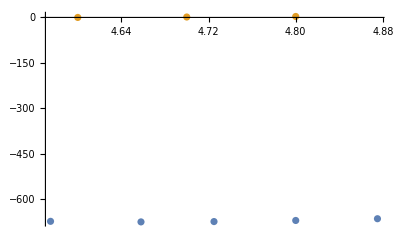

```mathematica
ListPlot[{lda,qmc}]
```

```mathematica
qmc
```

{{4.6,-972.786},{4.7,-971.39},{4.8,-969.567}}

```mathematica
ldaref=Transpose@{(Transpose[normal[[1]]][[1]])^(1/3)/2,Transpose[normal[[1]]][[2]]-Interpolation[lda][4.6]}
```

{{4.575,0.969451},{4.658,-0.901173},{4.725,0.200051},{4.8,3.81303},{4.875,9.59594}}

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

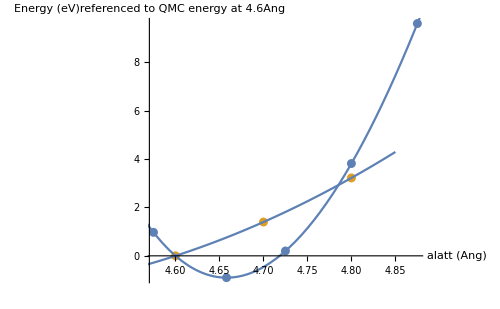

```mathematica
Show[ListPlot[{ldaref,qmc},PlotStyle->{"Thick"}],Plot[Interpolation[lda][x]-Interpolation[lda][4.6],{x,4.55,4.9}],Plot[Interpolation[qmc][x],{x,4.55,4.85}],AxesLabel->{"alatt (Ang)","Energy (eV)referenced \nto QMC energy at 4.6Ang"},ImageSize->500]
```